Your Title Here

```mathematica
f1=203.5;f2=302.7;
f3[x_]:=-1722.2*x^2-75.783*x+513.11;
(*f4[x_]:=-2008.9*x^2+3258.9*x-782.86;*)
f4[x_]:=-1928*x^2+3186*x-766.6;
f5[x_]:=-1929*x^2+1942.5*x-20.195;
f6[x_]:=-6655.1*x^2+13526*x-6250;
```

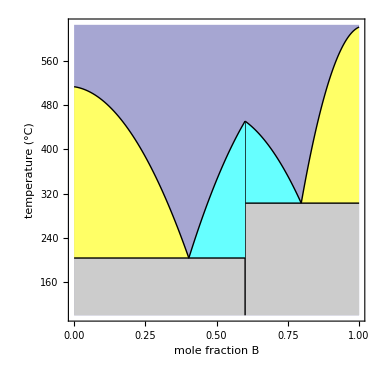

```mathematica
diagram=Show[
Graphics@{Directive[Darker[Blue,0.5],Opacity@0.35],Rectangle[{0,100},{1,625}]},
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->None,Filling->#3,FillingStyle->#4]&@@@{{Piecewise[{{f1,x<0.6},{f2,0.6<x}}],{0,1},100,GrayLevel@0.8},{f3[x],{0,0.403},f1,RGBColor[1,1,0.4]},{f4[x],{0.403,0.6},f1,RGBColor[0.4,1,1]},{f5[x],{0.6,0.797},f2,RGBColor[0.4,1,1]},{f6[x],{0.797,1},f2,RGBColor[1,1,0.4]}},
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->{Thick,Black}]&@@@{{f1,{0,0.6}},{f2,{0.6,1}},{f3[x],{0,0.403}},{f4[x],{0.403,0.6}},{f5[x],{0.6,0.797}},{f6[x],{0.797,1}}},
Graphics@{Thick,Line[{{0.6,100},{0.6,f5[0.6]}}]},
PlotRange->{{0,1},{100,625}},PlotRangePadding->None,Axes->None,Frame->True,FrameLabel->{Style["mole fraction B",17],Style["temperature (°C)",17]},LabelStyle->{14,Black},ImageSize->380,AspectRatio->1]
```

```mathematica
newEq3=Module[{fA0,f,sol},
fA0[x_]:=-1722.2*x^2-75.783*x+513.11;(*3*)
f[x_]:=α*x^2+β*x+χ;
sol=Quiet@Solve[f[0]==fA0[0]∧f[0.2]==fA0[0.2]∧f[0.4]==f1,{α,β,χ}][[1]];
f[x]/.sol]
```

513.11-66.421 x-1769.01 x^2

```mathematica
newEq4=Module[{fA0,fB0,f,sol},
fA0[x_]:=-2008.9*x^2+3258.9*x-782.86;(*eq4*)
fB0[x_]:=-1929*x^2+1942.5*x-20.195;(*eq5*)
f[x_]:=α*x^2+β*x+χ;
sol=Quiet@Solve[f[0.4]==f1∧f[0.5]==fA0[0.5]∧f[0.6]==fB0[0.6],{α,β,χ}][[1]];
f[x]/.sol]
```

-703.61+2955.07 x-1718.25 x^2

```mathematica
newEq5=Module[{fA0,f,sol},
fA0[x_]:=-1929*x^2+1942.5*x-20.195;(*eq5*)
f[x_]:=α*x^2+β*x+χ;
sol=Quiet@Solve[f[0.6]==Evaluate[newEq4/.x->0.6]∧f[0.7]==fA0[0.7]∧f[0.8]==f2,{α,β,χ}][[1]];
f[x]/.sol]
```

52.36+1717.92 x-1756.25 x^2

```mathematica
newEq6=Module[{fA0,f,sol},
fA0[x_]:=-6655.1*x^2+13526*x-6250;(*eq6*)
f[x_]:=α*x^2+β*x+χ;
sol=Quiet@Solve[f[0.8]==f2∧f[0.9]==fA0[0.9]∧f[1]==fA0[1],{α,β,χ}][[1]];
f[x]/.sol]
```

-6647.62+14365.4 x-7096.9 x^2

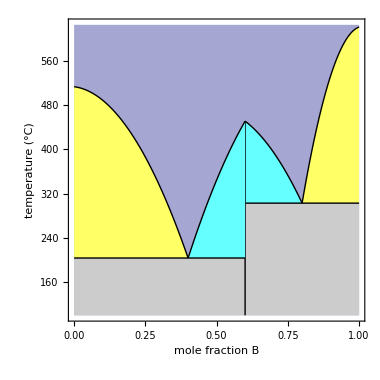

```mathematica
Show[
Graphics@{Directive[Darker[Blue,0.5],Opacity@0.35],Rectangle[{0,100},{1,625}]},
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->None,Filling->#3,FillingStyle->#4]&@@@{{Piecewise[{{f1,x<0.6},{f2,0.6<x}}],{0,1},100,GrayLevel@0.8},
{newEq3,{0,0.4},f1,RGBColor[1,1,0.4]},
{newEq4,{0.4,0.6},f1,RGBColor[0.4,1,1]},
{newEq5,{0.6,0.8},f2,RGBColor[0.4,1,1]},
{newEq6,{0.8,1},f2,RGBColor[1,1,0.4]}},
Plot[#1,Evaluate@Flatten@{x,#2},PlotStyle->{Thick,Black}]&@@@{{f1,{0,0.6}},{f2,{0.6,1}},
{newEq3,{0,0.4}},
{newEq4,{0.4,0.6}},
{newEq5,{0.6,0.8}},
{newEq6,{0.8,1}}},
Graphics@{Thick,Line[{{0.6,100},{0.6,f5[0.6]}}]},
PlotRange->{{0,1},{100,625}},PlotRangePadding->None,Axes->None,Frame->True,FrameLabel->{Style["mole fraction B",17],Style["temperature (°C)",17]},LabelStyle->{14,Black},ImageSize->380,AspectRatio->1]
```





```mathematica
Manipulate[XXXX,{}]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX